```mathematica
(*Import the video and set videoFrames to the image list of frames *)

filename="E:\\Cavendish\\runs\\run1.MOV";
frames=Import[filename,"ImageList"];
```

```mathematica
(*Get video dimensions for cropping*)
Manipulate[ImageTake[frames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

```mathematica
(*Cropping the image *)
length=Length[frames];
ymin=230;
ymax=370;
xmin=1;
xmax=1920;
croppedFrames=Table[ImageTake[frames[[i]],{ymin,ymax},{xmin,xmax}],{i,length}];
```

```mathematica
(*Show crop*)
```

```mathematica
croppedFrames[[1]]
```

-Graphics-

```mathematica
length
```

714

```mathematica
(*Use binarize to create a binary image set*)
```

```mathematica
binarizedFrames=Table[Binarize[croppedFrames[[i]],.5],{i,length}];
newBinarizedFrames=Table[DeleteSmallComponents[binarizedFrames[[i]]],{i,length}];
```

```mathematica
(*Get coordinates for the pixels*)
```

```mathematica
help=Table[ComponentMeasurements[newBinarizedFrames[[i]],"Centroid"],{i,length}]//Values;
xvals=Flatten[help[[;;,;;,1]]];
yvals=Flatten[help[[;;,;;,2]]];
```

```mathematica
(*Plot*)
```

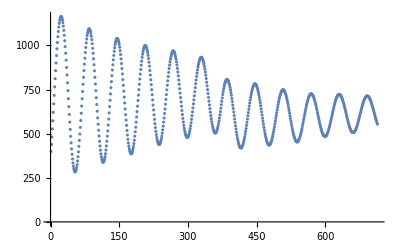

```mathematica
ListPlot[Transpose[xvals]]
```

```mathematica
run1data=Transpose@{xvals}

Export["D:\\Cavendish\\runs\\run1data.csv",run1data,"CSV"]
```

{{398.5},{438.7},{481.},{526.3},{572.929},{620.786},{668.833},{717.056},{764.875},{811.5},{857.},{900.375},{941.955},{980.786},{1016.63},{1049.33},{1078.79},{1103.5},{1124.63},{1141.5},{1153.79},{1161.},{1164.},{1162.3},{1155.9},{1144.7},{1129.1},{1109.},{1085.38},{1057.5},{1026.5},{992.611},{955.5},{916.375},{875.125},{832.5},{788.},{743.5},{698.167},{652.929},{608.786},{565.5},{524.},{484.75},{448.},{413.7},{383.147},{355.833},{333.3},{314.5},{299.833},{289.833},{284.167},{283.833},{287.833},{295.5},{307.833},{324.5},{345.3},{369.},{397.167},{428.},{461.3},{497.5},{535.5},{574.7},{615.333},{656.5},{697.786},{739.},{779.8},{819.214},{857.333},{893.8},{927.6},{959.833},{988.375},{1014.17},{1036.67},{1056.21},{1071.21},{1082.61},{1090.25},{1094.},{1093.63},{1089.},{1080.5},{1068.2},{1052.21},{1032.64},{1009.79},{983.5},{955.25},{924.167},{890.5},{855.929},{819.214},{781.125},{743.167},{703.357},{665.375},{626.833},{589.3},{553.5},{519.25},{486.833},{456.7},{430.167},{406.167},{385.3},{368.167},{355.},{345.5},{339.5},{337.75},{340.167},{346.},{355.833},{369.333},{386.214},{407.167},{430.5},{456.7},{485.5},{515.5},{548.7},{582.5},{617.333},{653.3},{689.125},{724.955},{760.227},{794.944},{828.5},{860.2},{890.},{918.1},{943.5},{966.389},{986.5},{1003.9},{1017.39},{1028.5},{1035.64},{1039.3},{1039.3},{1035.9},{1029.36},{1019.39},{1006.17},{989.5},{970.5},{948.},{923.625},{897.167},{868.5},{838.5},{806.5},{773.944},{740.5},{707.},{673.357},{639.833},{607.5},{576.7},{546.7},{517.9},{492.},{468.},{447.167},{428.5},{413.333},{401.3},{392.833},{387.7},{385.567},{386.333},{392.},{400.},{411.3},{426.5},{443.5},{462.7},{485.5},{510.5},{536.25},{564.75},{594.5},{624.7},{655.5},{687.5},{718.5},{749.389},{779.833},{809.3},{837.5},{863.375},{888.5},{910.864},{932.192},{950.},{964.9},{977.875},{988.},{995.071},{998.9},{999.643},{997.611},{992.611},{984.625},{973.333},{960.071},{943.773},{925.389},{904.682},{882.5},{857.7},{832.},{805.333},{777.5},{749.},{720.125},{690.75},{661.833},{634.167},{607.},{580.75},{556.5},{534.3},{513.071},{494.5},{478.3},{465.167},{454.},{446.},{441.25},{438.722},{439.3},{443.5},{449.7},{459.5},{471.167},{485.833},{502.5},{521.5},{542.5},{564.929},{588.7},{614.333},{639.833},{666.75},{694.},{721.5},{748.},{774.},{799.375},{823.667},{847.},{869.071},{888.5},{906.833},{922.833},{936.5},{947.75},{957.},{963.667},{967.357},{969.167},{967.5},{963.214},{956.5},{947.75},{936.25},{922.75},{907.389},{889.5},{870.167},{849.5},{827.071},{803.7},{779.955},{754.833},{729.786},{704.5},{680.},{655.5},{631.214},{608.5},{586.5},{566.3},{547.5},{531.1},{516.5},{504.1},{494.1},{486.833},{481.5},{478.5},{478.5},{481.},{485.833},{492.7},{503.},{514.5},{528.5},{544.5},{561.5},{581.357},{601.5},{623.1},{645.667},{668.5},{691.214},{714.5},{737.875},{760.833},{783.},{804.3},{824.7},{843.214},{860.929},{876.75},{890.786},{903.167},{913.278},{921.389},{927.25},{931.115},{932.682},{931.833},{928.682},{923.},{915.667},{906.},{894.611},{881.214},{865.786},{849.375},{831.5},{812.3},{791.611},{770.875},{749.389},{727.214},{705.5},{683.833},{662.333},{641.5},{621.357},{602.3},{584.7},{568.},{552.667},{539.929},{528.9},{519.5},{512.3},{507.071},{504.333},{503.833},{505.5},{509.},{515.071},{523.},{533.},{544.5},{557.7},{572.5},{588.7},{606.375},{624.7},{643.929},{664.},{683.643},{702.667},{721.375},{737.5},{752.5},{766.3},{778.25},{787.625},{795.5},{801.227},{805.5},{807.1},{806.214},{804.},{799.5},{793.25},{784.625},{774.125},{762.},{748.8},{733.5},{717.5},{699.5},{681.5},{661.75},{642.625},{622.9},{602.833},{582.7},{563.5},{544.3},{526.125},{508.7},{492.7},{477.5},{464.5},{452.3},{442.},{433.25},{426.833},{422.},{419.75},{419.167},{420.3},{424.167},{428.5},{435.7},{444.5},{455.7},{467.5},{480.833},{495.833},{512.167},{528.5},{546.333},{563.7},{582.7},{601.},{619.375},{638.214},{655.833},{673.071},{689.786},{705.667},{720.7},{733.214},{744.955},{755.214},{764.},{771.25},{777.},{780.136},{782.167},{781.75},{779.833},{776.071},{770.5},{763.5},{754.6},{744.389},{732.5},{720.357},{705.7},{690.75},{674.9},{658.},{640.5},{623.1},{605.5},{587.5},{570.5},{553.167},{536.25},{520.833},{506.},{492.7},{480.},{469.833},{459.5},{452.},{444.5},{439.682},{436.7},{435.5},{435.5},{437.7},{442.},{447.5},{454.7},{462.7},{472.5},{484.3},{496.3},{510.},{524.},{539.},{554.5},{570.5},{586.357},{602.5},{618.25},{634.167},{649.},{663.9},{677.5},{690.786},{702.},{712.944},{722.389},{730.278},{737.125},{742.389},{745.722},{748.25},{749.},{748.},{744.833},{740.5},{734.75},{728.056},{719.667},{709.786},{698.9},{687.3},{675.},{660.786},{646.5},{631.75},{616.5},{601.5},{585.929},{571.5},{556.7},{542.},{528.5},{515.333},{503.75},{492.7},{483.},{475.},{467.7},{461.5},{457.7},{454.5},{452.9},{453.167},{454.7},{458.786},{462.5},{469.},{475.7},{484.3},{494.},{504.1},{515.5},{527.3},{540.333},{554.3},{567.5},{581.5},{595.5},{609.},{623.},{636.},{648.5},{661.3},{671.9},{682.5},{692.3},{700.5},{708.625},{714.167},{718.833},{722.875},{724.955},{725.4},{725.278},{723.5},{720.5},{716.},{710.625},{703.357},{696.167},{687.5},{677.5},{667.},{655.875},{643.5},{632.},{619.375},{606.864},{594.167},{582.},{569.5},{557.7},{546.7},{535.5},{526.},{517.},{508.5},{501.3},{495.7},{490.7},{487.},{484.833},{483.7},{483.7},{485.5},{488.},{492.},{497.},{503.3},{510.3},{518.3},{527.5},{537.7},{547.929},{560.},{570.7},{582.5},{594.7},{606.864},{619.214},{630.786},{642.5},{653.5},{664.7},{674.3},{683.833},{692.},{699.357},{706.},{711.357},{716.},{719.071},{721.5},{722.625},{722.625},{721.214},{718.5},{714.5},{710.7},{704.643},{697.7},{690.786},{681.667},{672.5},{663.3},{653.},{642.5},{631.375},{620.5},{609.1},{598.},{586.786},{576.7},{565.9},{556.5},{547.5},{539.},{531.},{524.5},{518.3},{514.},{510.25},{507.7},{506.1},{506.1},{506.3},{508.5},{511.3},{515.333},{520.3},{526.357},{533.333},{540.5},{549.},{558.},{567.833},{577.5},{587.929},{598.5},{609.},{619.5},{630.25},{640.},{649.875},{659.5},{668.5},{676.5},{684.786},{690.75},{697.3},{702.5},{706.5},{710.056},{711.833},{713.375},{713.357},{712.4},{710.625},{708.},{703.5},{699.},{693.1},{687.},{680.3},{671.667},{664.},{654.5},{645.5},{636.167},{626.333},{616.375},{606.7},{597.125},{587.5},{578.5},{569.929},{561.5},{554.3}}

D:\Cavendish\runs\run1data.csv